## quantum

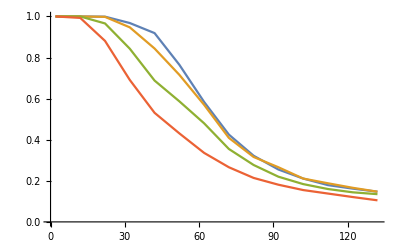

{{2.40173,0.1,{{2,1},{12,1},{22,999/1000},{32,121/125},{42,919/1000},{52,153/200},{62,73/125},{72,17/40},{82,161/500},{92,51/200},{102,211/1000},{112,179/1000},{122,81/500},{132,147/1000}}},{3.21421,0.2,{{2,1},{12,1},{22,499/500},{32,947/1000},{42,211/250},{52,179/250},{62,57/100},{72,409/1000},{82,79/250},{92,133/500},{102,211/1000},{112,47/250},{122,83/500},{132,147/1000}}},{5.24215,0.5,{{2,1},{12,1},{22,483/500},{32,843/1000},{42,86/125},{52,587/1000},{62,12/25},{72,71/200},{82,277/1000},{92,11/50},{102,23/125},{112,4/25},{122,18/125},{132,27/200}}},{8.30862,1.,{{2,1},{12,993/1000},{22,881/1000},{32,691/1000},{42,531/1000},{52,431/1000},{62,42/125},{72,133/500},{82,107/500},{92,181/1000},{102,31/200},{112,69/500},{122,121/1000},{132,21/200}}}}

```mathematica
Clear["Global`*"]
kHz=10^3;
nm=10^-9;
mK=10^-3;
uK=10^-6;
us=10^-6;
kB=1.38064852 10^-23;
ℏ=1.0545718 10^-34;
amu=1.66054 10^-27;
m=132.90545 amu;

(*Cs, our expt:*)
λtrap=970 nm;
m=132.90545 amu;
scale=1;
α=1;
{Ttrap,frad,fax}={α^2 1.2mK ,α 120kHz,α 20kHz};
ftrap={frad,frad,fax};
Utrap = kB Ttrap;

w0=√(Utrap/(ftrap[[1]]^2 m π^2)); (*0.67, 133 amu, 71kHz gives 917 nm*)
w[z_]:=w0√(1+((λtrap z)/(π w0^2))^2);
U[r_]:=Utrap(1-w0^2/w[r[[3]]]^2 Exp[-2 (r[[1]]^2+r[[2]]^2)/w[r[[3]]]^2]);
Δt=Range[2,140,10]us;
nSim=1000; (*number of realizations*)

TList= (ℏ 2π f)/(kB Log[1/nbar+1])/.f->frad/.nbar->{.1,.2,.5,1};

mcTOFfitQM=Reap[
Do[(*loop over TList*)
coordsInit=Reap[
Do[(*loop nSim times*)
coordsInitSingle=Reap[
Do[(*loop over 3 axes*)
nbar=1/(Exp[(ℏ 2π f)/(kB T)]-1);
nCutoff=10 Ceiling[nbar];
Pn=Table[nbar^n/(nbar+1)^(n+1),{n,0,nCutoff}]; (*probability distribution*)
Cn=Accumulate[Pn]; (*cumulative distr*)

(*sample n from a probability distribution Pn*)
(*compare random number to cumulative distribution. put 1 if positive, 0 if negative.*)
listpn=Boole[Positive[#]]&/@(RandomReal[]-Cn);
(*the total of this list gives the corresponding n*)
n=Total[listpn];


ϵn=(n+1/2)ℏ 2π f;

(*randomly sample mixing angle b/t v and x*)
θ=RandomReal[2π];
xtemp=(√ϵn Sin[θ])/(√(1/2 m)(2π f));
vtemp=(√ϵn Cos[θ])/(√(1/2 m)); 

coordstemp={xtemp,vtemp};

Sow[coordstemp],
{f, ftrap}
]
][[2,1]];

(*list of the form {{x,y,z},{vx,vy,vz}}*)
coordsInitSingle=Transpose[coordsInitSingle];
Sow[coordsInitSingle]
,{j,nSim}]
][[2,1]];

rInit=Transpose[coordsInit][[1]];
vInit=Transpose[coordsInit][[2]];
KInit=m/2 Norm[#]^2&/@vInit;

(*sort by realizations. ie each list scans thru all Δt for a single realization*)
rFin=Transpose[rInit+vInit #&/@Δt];
PFin=U[#]&/@#&/@rFin;

EFin=(#1+#2)&[PFin,KInit];
SurvProb=Thread[{Δt/us,scale Total[#]&/@Transpose[Boole[Positive[Utrap-EFin]]]/Length[rInit]}];
nbar0=1/(Exp[(ℏ 2π f)/(kB T)]-1)/.f->frad;
Sow[{T/uK,nbar0,SurvProb}]
,{T,TList}]
][[2,1]];
ListPlot[mcTOFfitQM[[;;,3]],Joined->True]
mcTOFfitQM
```

## RowBox[{"{", RowBox[{"132", ",", FractionBox["53", "200"]}], "}"}], ",", RowBox[{"{", RowBox[{"142", ",", FractionBox["28", "125"]}], "}"}], ",",

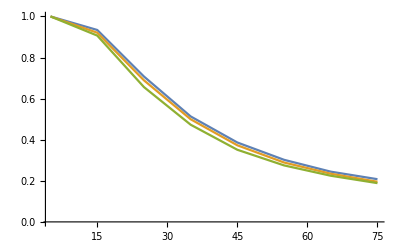

18.7191 | 3.2 | 0.2078
19.7432 | 3.4 | 0.1953
20.7666 | 3.6 | 0.1887

```mathematica
Clear["Global`*"]
(*units and constants for trap depth mostly*)
kHz=10^3;
nm=10^-9;
mK=10^-3;
uK=10^-6;
us=10^-6;
kB=1.38064852 10^-23;
ℏ=1.0545718 10^-34;
amu=1.66054 10^-27;
scale=1;

(*Cs, our expt:*)
λtrap=970 nm;
m=132.90545 amu;
scale=1;
{Ttrap,frad,fax}={2(75/70.7)^2.67mK ,√2 75/70.7 70.7kHz,√2 75/70.7 11.8kHz};

Utrap = kB Ttrap;
ftrap={frad,frad,fax(*√((λtrap^2 m frad^4)/(2 Utrap))*)} ;
ωtrap=2π ftrap;
w0=√(Utrap/(ftrap[[1]]^2 m π^2)); (*0.67, 133 amu, 71kHz gives 917 nm*)
w[z_]:=w0√(1+((λtrap z)/(π w0^2))^2);
U[r_]:=Utrap(1-w0^2/w[r[[3]]]^2 Exp[-2 (r[[1]]^2+r[[2]]^2)/w[r[[3]]]^2]);
Δt=Range[5,80,10]us;
nSim=10000; (*number of realizations*)
TList=(ℏ 2π f)/(kB Log[1/nbar+1])/.f->frad/.nbar->Range[3.2,3.6,.2];Range[25,35,1]uK; 
mcTOFfitCLASS=Reap[
Do[
Δr=√((kB T)/m)1/ωtrap;
Δv=√((kB T)/m){1,1,1}; 

rInit=Transpose[RandomVariate[NormalDistribution[0,#],nSim]&/@Δr];
vInit=Transpose[RandomVariate[NormalDistribution[0,#],nSim]&/@Δv];

KInit=m/2 Norm[#]^2&/@vInit;
PInit=U[#]&/@rInit;
 
(*probability of realization*)

(*MBProb=Exp[-#/(kB T)]/(kB T)&/@(KInit+PInit);
MBProb=2 √(#/π)(1/(kB T))^(3/2)Exp[-#/(kB T)]&/@(KInit+PInit);
MBProb=Exp[-#/(kB T)]&/@(KInit+PInit);
*)
MBProb=2 √(#/π)(1/(kB T))^(3/2)Exp[-#/(kB T)]&/@(KInit+PInit);
(*IF TRUE THEN KEEP (SAMPLE MB DISTR)*)
KeepQ=Positive[#1-#2]&@@{
MBProb,
RandomReal[1,nSim]
};
(*list of positions to keep*)
keep=Flatten[Position[KeepQ,True]];

rInit=rInit[[keep]];
vInit=vInit[[keep]];
KInit=KInit[[keep]];

(*sort by realizations. ie each list scans thru all Δt for a single realization*)
rFin=Transpose[rInit+vInit #&/@Δt];
PFin=U[#]&/@#&/@rFin;

EFin=(#1+#2)&[PFin,KInit];
SurvProb=Thread[{Δt/us,scale Total[#]&/@Transpose[Boole[Positive[Utrap-EFin]]]/Length[keep]}];
(*
sigma=1.Flatten[Differences[#]&/@survErr];
chiSquare=Total[(SurvProb-survival)^2[[;;,2]]/sigma^2];
Sow[{T/uK,SurvProb,chiSquare}]
*)
nbar0=1/(Exp[(ℏ 2π f)/(kB T)]-1)/.f->frad;
Sow[{T/uK,nbar0,SurvProb}]
,{T,TList}]
][[2,1]];


Show[{
ListPlot[mcTOFfitCLASS[[;;,3]],Joined->True,PlotRange->All]

}
]
Thread[{
mcTOFfitCLASS[[;;,1]],
mcTOFfitCLASS[[;;,2]],
mcTOFfitCLASS[[;;,3]][[;;,-1]][[;;,2]]1.

}]//TableForm
```

```mathematica
1/(Exp[(ℏ 2π f)/(kB T)]-1)/.f->frad/.T->33uK
```

5.99568

```mathematica
kB  T= □/Log[1/nbar+1]/.f->frad
```

```mathematica
frad/kHz
```

106.066

```mathematica
fax
```

17702.7

```mathematica
1/uK(ℏ 2π f)/(kB Log[1/nbar+1])/.f->frad/.nbar->3.4
```

19.7432

```mathematica
mcTOFfitCLASS 1.
```

{{18.7191,3.2,{{5.,1.},{15.,0.9342},{25.,0.7076},{35.,0.5134},{45.,0.3864},{55.,0.3022},{65.,0.2445},{75.,0.2078}}},{19.7432,3.4,{{5.,0.9999},{15.,0.9209},{25.,0.6892},{35.,0.4997},{45.,0.3729},{55.,0.2891},{65.,0.2346},{75.,0.1953}}},{20.7666,3.6,{{5.,1.},{15.,0.9069},{25.,0.6563},{35.,0.4731},{45.,0.3511},{55.,0.275},{65.,0.2247},{75.,0.1887}}}}